```mathematica
SetDirectory["~/doc/research/first_order_singularities/paper"];
```

```mathematica
<<IsingScalingFunction`
```

```mathematica
PrepareArgument[Data[2]]
```

{1.14841,0.989667,5.08831,-0.0114295,-0.172824,{-0.310184,0.247454},{0.373691,-0.0216363}}

```mathematica
Data[2]["θ0"]
```

1.14841

```mathematica
data2={θ0->1.14841,θYL->0.989667,CYL->-0.172824,G[1]->-0.310183,G[2]->0.247454,g[0]->0.373691,g[1]->-0.0216363}
```

{θ0→1.14841,θYL→0.989667,CYL→-0.172824,G[1]→-0.310183,G[2]→0.247454,g[0]→0.373691,g[1]→-0.0216363}

```mathematica
prep2={θ0,θYL,ruleB[θ0,{g[0],g[1]}],ruleAL[θ0,{g[0],g[1]}],CYL,{G[1],G[2]},{g[0],g[1]}}/.data2
```

{1.14841,0.989667,5.08816,-0.0114291,-0.172824,{-0.310183,0.247454},{0.373691,-0.0216363}}

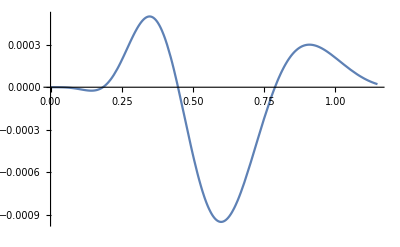

```mathematica
Plot[Evaluate@Last[(DScriptF0DηList@@PrepareArgument[Data[6]])[6,θ]],{θ,0,1.1483}]
```

```mathematica
Solve[{tt==R(θ^2-1),h==R^(15/8)g[Data[2]["θ0"],Data[2]["gs"]][θ]},{R,h}]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{R→tt/(-1.+θ^2),h→-0.288579 tt θ (-(1. tt)/(1.-1. θ^2))^(7/8)+0.0164056 tt θ^3 (-(1. tt)/(1.-1. θ^2))^(7/8)-(0.0851121 tt θ (-(1. tt)/(1.-1. θ^2))^(7/8))/(1.-1. θ^2)}}

```mathematica
InverseCoordinates[θ0_,gs_][ut_,uh_]:=FindRoot[{ut==R(θ^2-1),uh==Abs[R]^(15/8)g[θ0,gs][θ]},{{R,2,0,10^8},{θ,Sign[uh]0.5,-Data[2]["θ0"],Data[2]["θ0"]}}]
```

```mathematica
InverseCoordinates[Data[2]["θ0"],Data[2]["gs"]][0.8,0.01]
```

{R→2.5551,θ→1.14591}

```mathematica
Solve[{tt==R(θ^2-1),h==R^Δ g[θ]},{R,θ}]
```

$Aborted

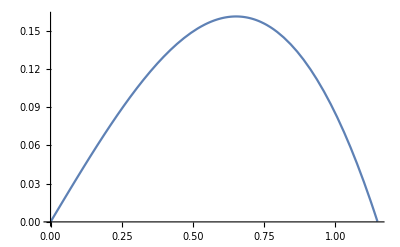

```mathematica
Plot[Evaluate[g[θ0,{g[0],g[1]}][θ]/.data2],{θ,0,1.148}]
```

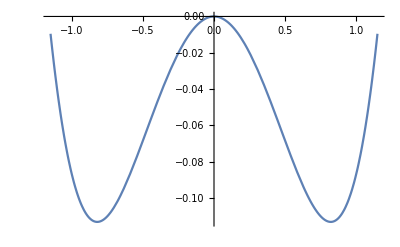

```mathematica
Plot[(uf@@Most[prep2])[1,θ],{θ,-1.148,1.148}]
```

```mathematica
dat=Flatten[Table[{ut[R,θ],uh[θ0,{g[0],g[1]}][R,θ],-(DufDuh@@prep2)[1][R,θ]}/.data2,{R,0.05,2,0.05},{θ,-1.14841,1.14841,0.05}],1];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
ListPlot3D[dat]
```

-Graphics3D-

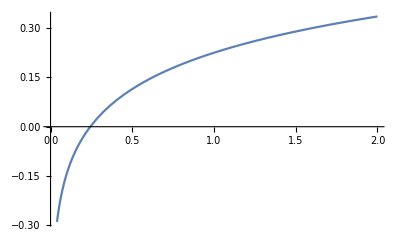

```mathematica
Plot[Evaluate[(DufDut@@prep2)[2][R,0.1]],{R,0,2}]
```

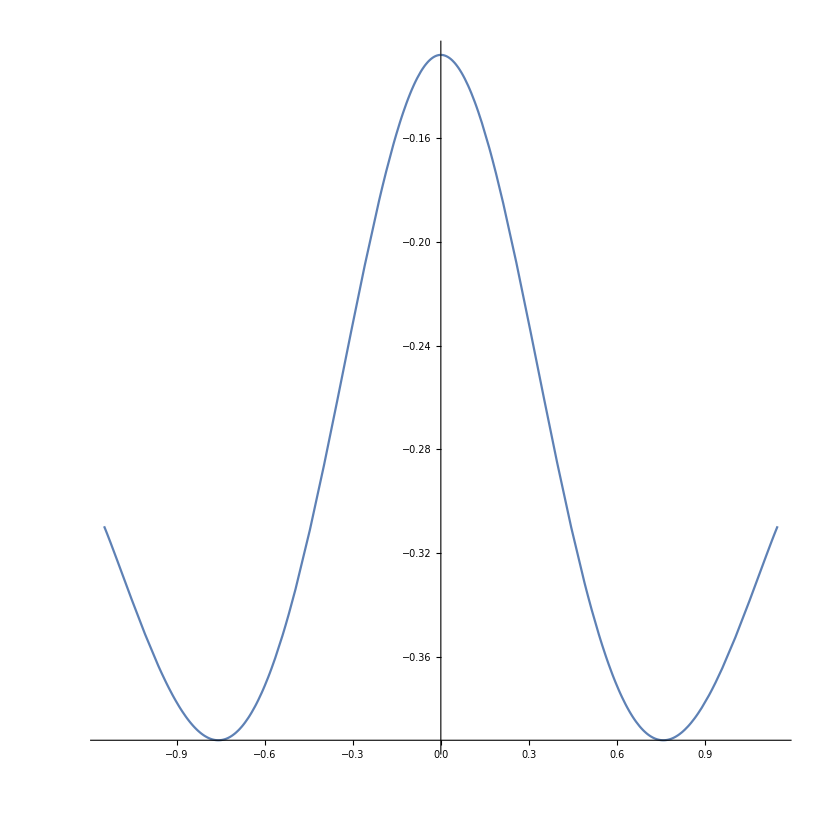

```mathematica
ParametricPlot[{θ,Evaluate[(DufDut@@prep2)[2][.1,θ]]},{θ,-1.148,1.148},AspectRatio->1]
```

```mathematica
dGdξ
```

```mathematica
(dΦdηList@@prep2)[0,1]
```

{-1.19741+0. ⅈ}

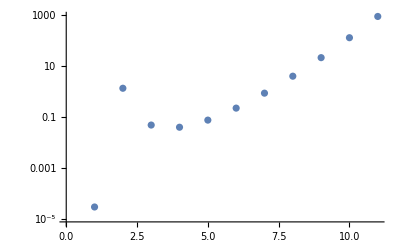

```mathematica
ListLogPlot[Abs[(DScriptFPlusMinusDξθ0List@@prep2)[10]]]
```

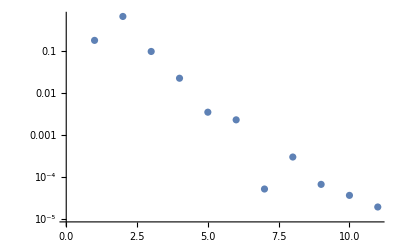

```mathematica
ListLogPlot[Abs[(DScriptF0DηList@@prep2)[10,0.5]]]
```